## Text Analysis

```mathematica
text="I am feeling peaceful. Watched the sun rise and heard the birds chirp a beautiful good morning song. I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing. Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring. Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.";
```

```mathematica
sentences = TextCases[text,"Sentence"]
```

{I am feeling peaceful.,Watched the sun rise and heard the birds chirp a beautiful good morning song.,I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing.,Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring.,Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.}

```mathematica
ClearAll[i]
```

```mathematica
(* NOT WORKING :(  *)
(* take in paragraph, output how many sentences are respectively Positive, Negative, Neutral *)
CountSentiments[ text_String ] := Module[{sentences , classifyResults, countPos,countNeg,countNeut,posEval,negEval,neutEval},

countPos = 0;
countNeg = 0;
countNeut = 0;

sentences = TextCases[text, "Sentence"];

classifyResults = Classify["Sentiment", sentences, "Probabilities"];

posEval = classifyResults[[All,"Positive"]];
negEval = classifyResults[[All,"Negative"]];
neutEval = classifyResults[[All,"Neutral"]];

For[i=1,i≤ Length[posEval],i++, If[posEval[[i]] ≥ 0.3, countPos = countPos +1, Nothing ]];
For[i=1,i≤ Length[negEval],i++, If[negEval[[i]]≥ 0.3, countNeg = countNeg +1 ,Nothing]];
For[i=1,i≤ Length[neutEval],i++, If[neutEval[[i]]≥ 0.3, countNeut = countNeut +1 ,Nothing]];
{countPos,countNeg,countNeut}
	   
];
```

```mathematica
(* NOT WORKING :(  *)
(* take in paragraph, output how many sentences are respectively Positive, Negative, Neutral *)
countSentiments[ text_String ] := Module[{sentences , classifyResults, countPos,countNeg,countNeut, countsAssociation},

sentences = TextCases[text, "Sentence"];

classifyResults = Classify["Sentiment", sentences];

countsAssociation = Counts [classifyResults];

countPos = countsAssociation["Positive"];
countNeg = countsAssociation["Negative"];
countNeut = countsAssociation["Neutral"];
{countPos, countNeg, countNeut} /. _Missing -> 0

];
```

```mathematica
(* NOT WORKING :(  *)
(* take in paragraph, output how many sentences are respectively Positive, Negative, Neutral *)
countSentimentsAssociation[ text_String ] := Module[{sentences , classifyResults, countPos,countNeg,countNeut, countsAssociation},

sentences = TextCases[text, "Sentence"];

classifyResults = Classify["Sentiment", sentences];

countsAssociation = Counts [classifyResults]


];


createPieChart [ text_String ] := PieChart[ countSentimentsAssociation[text],  ChartLabels -> Automatic];

createBarChart [ text_String ] := BarChart[ countSentimentsAssociation[text],  ChartLabels -> Automatic];
```

```mathematica
countSentiments["I am happy. I am sad. I am cold."]
```

{2,1,0}

```mathematica
countSentimentsAssociation["I am happy. I am sad. I am cold."]
```

<|Positive→2,Negative→1|>

```mathematica
PieChart[countSentimentsAssociation["I am happy. I am sad. I am cold."],  ChartLabels -> Automatic]
```

-Graphics-

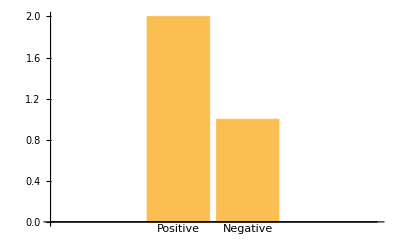

```mathematica
createBarChart [ "I am happy. I am sad. I am cold." ]
```

### Microsite

```mathematica
FormFunction
```

```mathematica
CloudDeploy[

FormPage[{{"text","Copy Past Your Diary:"} ->"String" ,
{"image","Copy Past Your selfie of the day:"} ->"Image"},

Column[{ createPieChart[#text],
Column[{Classify["FacialExpression", #image],#image}]
}]&,

AppearanceRules-> {"Title" -> "Hearty"}]

,"Hearty"
, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/clloo/Hearty]

```mathematica
Classify["FacialExpression", #image]
```

```mathematica
Face
```

### Other Stuff

```mathematica
testSentences = TextCases["I am happy. I am sad. I am cold.","Sentence"]
```

{I am happy.,I am sad.,I am cold.}

```mathematica
Classify["Sentiment", testSentences, "Probabilities"][[All,"Positive"]]
```

{0.915166,0.241839,0.496866}

```mathematica
CountSentiments["I am happy. I am sad. I am cold."]
```

{2,1,0}

```mathematica
PieChart[%]
```

-Graphics-

```mathematica
(* Make a list of only the Positive sentences in a paragraph. *)
PosSentences[ text_String ] := With[{sentences = TextCases[text, "Sentence"]},
posList = {};
posEval = Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]];

For[i=1,i≤ Length[posEval],i++, If[posEval≥ 0.5, AppendTo [posList,sentences[[i]] ,Nothing]];

posList;
];
```

```mathematica
PosSentences["I am happy. I am sad. I am cold."]
```

PosSentences[I am happy. I am sad. I am cold.]

```mathematica
(* Extract the verbs and nouns from only Positive sentences in a paragraph. *)
PosVerbsNouns[ text_String ] := With[{sentences = TextCases[text, "Sentence"]},

posVerbs = {};
posNouns = {};
posEval = Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]];

For[i=1 , i≤ Length[posEval], i++, If[posEval ≥ 0.5,
													If[Map[PartOfSpeech, sentences[[i]][[1]] == "Noun", AppendTo[posNouns, sentences[[i]], Nothing],
																																					Nothing]]]];
For[i=1 , i≤ Length[posEval], i++, If[posEval ≥ 0.5,
													If[Map[PartOfSpeech, sentences[[i]][[1]]]] == "Verb", AppendTo[posVerbs, sentences[[i]], Nothing],
																																					Nothing] ]]];																																					
						
posVerbs;
posNouns;
]
```

```mathematica
(* Make graph of probabilities *)
```

```mathematica
(* Make graph of categories of words like in the text analyis lecture *)
```

```mathematica
(* From text analysis lecture code: Get a GloVe (Global Vectors) word embedding model and run it: *)
```

```mathematica
glove = NetModel[
"GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

```mathematica
glove[text]
```

{{-0.046539,0.61966,0.56647,-0.46584,-1.189,0.44599,0.066035,86,0.28374,-0.70931,0.15003,-0.2154,-0.37616,-0.032502,0.8062},92,{1}}
 |  |  |  |

```mathematica
Dimensions[text]
```

{}

Last modified on: Tuesday, July 10, 2018 at 11:44

## Scratch Work

```mathematica
Counts[Classify["Sentiment",sentences]]
```

<|Positive→4,Negative→1|>

```mathematica
Mean@Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]]
```

0.7445

```mathematica
Classify["Sentiment", sentences, "Probabilities"][[All,"Neutral"]]
```

{0.113184,0.0337055,0.0497827,0.233479,0.138568}

```mathematica
Map[PartOfSpeech,{"dog","eat"}][[1]][[1]]
```

noun